## Canonicity factors

Creating proper inertia factors A_2 and A_3 from the value of A_1

```mathematica
ClearAll["Global`*"]
```

```mathematica
T[j_,gm_]:=1/(j(j+1))√3(√3 Cos[gm]+Sin[gm]);
TP[j_,gm_]:=1/(j(j+1))2 √3 Sin[gm];
S[I_,j_]:=(2I-1-2j)/(2I-1);
SP[I_,j_]:=(2j-1-2I)/(2j-1);
```

```mathematica
A3condition[A1_,I_,j_,V_,gm_]:=(SP[I,j]*A1-V*T[j,gm]);
A2condition[A1_,I_,j_,V_,gm_]:=(SP[I,j]*A1-V*TP[j,gm]);
```

```mathematica
A1=0.2;
I0=35/2;
j0=13/2;
V0=3;
gm0=25;
```

```mathematica
k1[I_,j_,A1_,A2_,A3_]:=(I^2*((2I-1)(A2-A1)+2j*A1)/((2I-1)(A3-A1)+2j*A1))^(1/4);
k1[35/2,j0,A1,2A1,5A1]
k1[35/2,j0,A1,5A1,2A1]
A2condition[A1,0.5,j0,V0,gm0*π/180]
A3condition[A1,0.5,j0,V0,gm0*π/180]
```

3.13507

5.58202

0.0932415

-0.029031

## Generate lists for numerical data

```mathematica
(*the data set for ordering A3>A2>A1 *)
k1data1=Table[{x,k1[x,j0,A1,2A1,5A1]},{x,0.5,45.5,2}];
(*the data set for ordering A2>A3>A1 *)
k1data2=Table[{x,k1[x,j0,A1,5A1,2A1]},{x,0.5,45.5,2}];
```

```mathematica
k1plot=ListPlot[{k1data1,k1data2},AspectRatio->0.8,Frame->True,Joined->True,PlotMarkers->{Automatic, Medium},FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick},{Blue,Thick}},PlotRange->Full,FrameLabel->{"I [ℏ]","k_1"},LabelStyle->{18,Bold,Black,FontFamily->"Arial"},ImageSize->380,PlotLegends->Placed[{"A_3>A_2>A_1","A_2>A_3>A_1"},{0.75,0.25}]];
k1fig=Show[k1plot,Graphics[{Magenta,Thick,Dashed,Line[{{13/2,0},{13/2,10}}]}],Graphics[{Green,HatchFilling[-1],Opacity[0.4],Rectangle[{-1,-1},{13/2,10}]}],Graphics[{Green,Opacity[0.15],Rectangle[{13/2,-1},{50,10}]}],Graphics[Inset[Style["I ≤ j",Black,Bold,FontFamily->"Palatino",21],Scaled[{0.08,0.8}]]],Graphics[Inset[Style["I ≥ j",Black,Bold,FontFamily->"Palatino",21],Scaled[{0.3,0.8}]]]];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/wobbling-frequency-algebraic/k1_factor.pdf",k1fig];
k1fig
```

-Graphics-

### k1[I_,j_,A1_,A2_,A3_]:=(I^2*((2I-1)(A2-A1)+2j*A1)/((2I-1)(A3-A1)+2j*A1))^(1/4);

```mathematica
A3extended[I_,j_,V_,gm_]:=SP[I,j]*A1-V*T[j,gm];
A2extended[I_,j_,V_,gm_]:=SP[I,j]*A1-V*TP[j,gm];
k2[I_,j_,A1_,A2_,A3_,V_,gm_]:=(j^2*((2j-1)(A2-A1)+2I*A1+V*(2j-1)/(j(j+1))2 √3 Sin[gm])/((2j-1)(A3-A1)+2I*A1+V*(2j-1)/(j(j+1))√3(√3 Cos[gm]+Sin[gm])))^(1/4);
A1
A2extended[I0,j0,V0,gm0*π/180]
A3extended[I0,j0,V0,gm0*π/180]
```

0.2

-0.473425

-0.595698

## Generate the numerical data

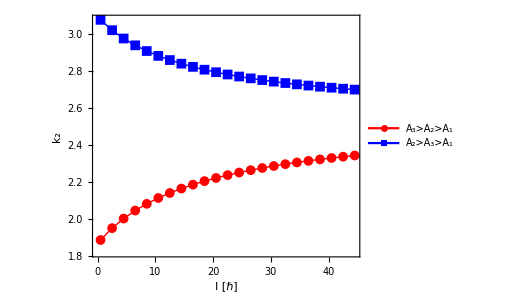

```mathematica
k2data1=Table[{x,k2[x,j0,A1,2A1,5A1,V0,gm0*π/180]},{x,0.5,45.5,2}];
k2data2=Table[{x,k2[x,j0,A1,5A1,2A1,V0,gm0*π/180]},{x,0.5,45.5,2}];
k2plot=ListPlot[{k2data1,k2data2},AspectRatio->0.8,Frame->True,Joined->True,PlotMarkers->{Automatic, Medium},FrameStyle->Directive[Black,Thick],PlotStyle->{{Red,Thick},{Blue,Thick}},PlotRange->Full,FrameLabel->{"I [ℏ]","k_2"},LabelStyle->{18,Bold,Black,FontFamily->"Arial"},ImageSize->380,PlotLegends->Placed[{"A_3>A_2>A_1","A_2>A_3>A_1"},{0.75,0.2}]];
k2plot
```